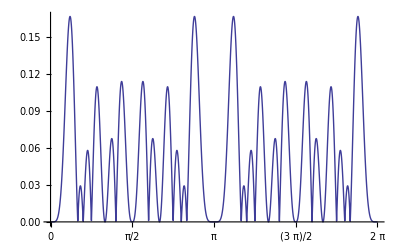

```mathematica
Plot[Product[Abs[Sin[k*t]],{k,1,6}],{t,0,2*Pi},Ticks->{Range[0,2*Pi,Pi/4],Automatic}]
```

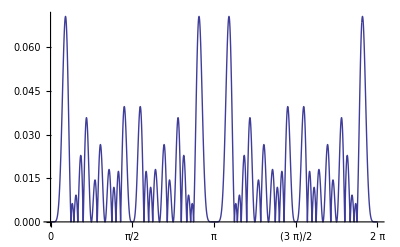

```mathematica
Plot[∏_(k=1)^8 Abs[Sin[k t]],{t,0,2 π},PlotPoints->100,MaxRecursion->10,Ticks->{Range[0,2 π,π/4],Automatic}]
```

```mathematica
Export["k8.pdf",%11,"PDF"]
```

k8.pdf

```mathematica
Directory[]
```

/Users/jordanbell

```mathematica
Export["sin6",%3,"PDF"]
```

sin6

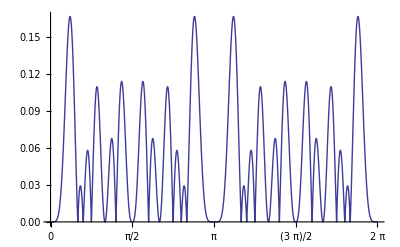

```mathematica
Plot[∏_(k=1)^6 Abs[Sin[k t]],{t,0,2 π},PlotPoints->100,MaxRecursion->10,Ticks->{Range[0,2 π,π/4],Automatic}]
```

```mathematica
Export["k6",%43,"PDF"]
```

k6

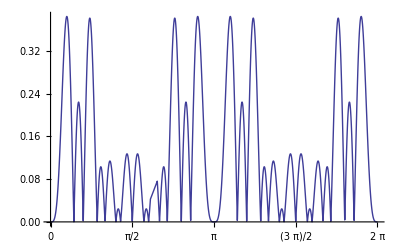

```mathematica
Plot[Product[Abs[Sin[Prime[k]*t]],{k,1,4}],{t,0,2*Pi},Ticks->{Range[0,2*Pi,Pi/4],Automatic}]
```

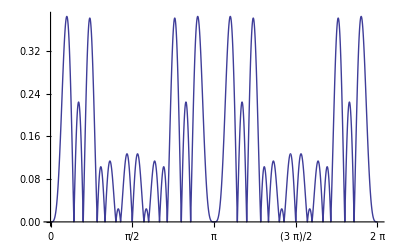

```mathematica
Plot[∏_(k=1)^4 Abs[Sin[Prime[k] t]],{t,0,2 π},PlotPoints->100,MaxRecursion->10,Ticks->{Range[0,2 π,π/4],Automatic}]
```

```mathematica
Export["prime4.pdf",%9,"PDF"]
```

prime4.pdf

```mathematica
Export["prime4.pdf",%7,"PNG"]
```

prime4.pdf

```mathematica
Export["prime4",%42,"PNG"]
```

prime4

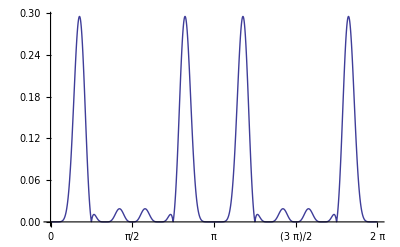

```mathematica
Plot[Product[Abs[Sin[Ceiling[Sqrt[k]]*t]],{k,1,10}],{t,0,2*Pi},Ticks->{Range[0,2*Pi,Pi/4],Automatic}]
```

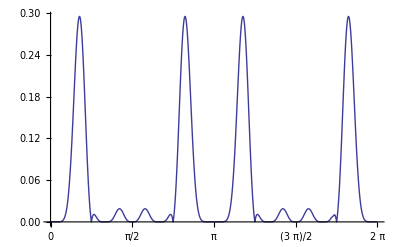

```mathematica
Plot[∏_(k=1)^10 Abs[Sin[Ceiling[√k] t]],{t,0,2 π},PlotPoints->100,MaxRecursion->10,Ticks->{Range[0,2 π,π/4],Automatic}]
```

```mathematica
Export["sqrt10",%44,"PDF"]
```

sqrt10

```mathematica
Sum[Ceiling[Sqrt[k]],{k,1,12}]
```

34

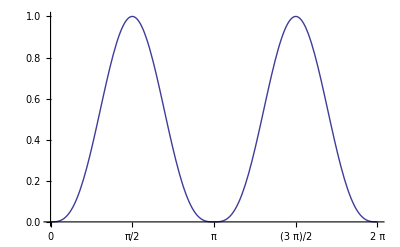

```mathematica
Plot[∏_(k=1)^3 Abs[Sin[t]],{t,0,2 π},PlotPoints->100,MaxRecursion->10,Ticks->{Range[0,2 π,π/4],Automatic}]
```

```mathematica
f1[w_?NumericQ]:=1/w*NIntegrate[Log[Sin[x]],{x,0,w}]
```

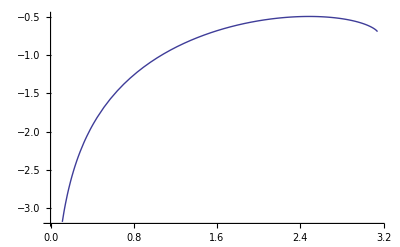

```mathematica
Plot[f1[x],{x,0,Pi}]
```

```mathematica
f2[w_?NumericQ]:=1/w*NIntegrate[Log[TriangleWave[x]],{x,0,w}]
```

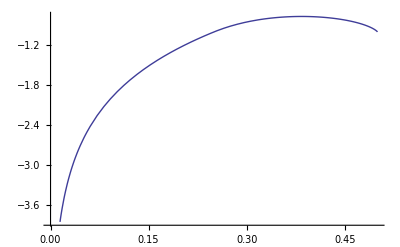

```mathematica
Plot[f2[x],{x,0,0.5}]
```